# Теория

## Одномерный случай

## Формулировка задачи

Рассмотрим систему линейных уравнений в матричнов виде

Y=X.A

где X∈ℝ^(n×m) , Y∈ℝ^n,A∈ℝ^m

Необходимо определить вектор A,зная X и Y .

## Простейщий случай

Если n=m и матрица X – невырожденная (det X ≠0),то вектор A определить точно

A=X^-1.Y

X^-1 – существует в силу невырожденности матрицы X

Проблема в том, что для матрицы X может не выполнятся n=mи она так же может быть вырожденной.

## Linear Least Squares (LLS)

### Функция ошибки

Для сравнения того,на сколько хорошо разные вектора A_1 и A_2  удовлетворяют уравнению (1),введём функцию ошибки φ

φ[A]=||Y-X.A||,

где ||Y||=√(∑_(i=1)^n Y_i^2)– евклидова норма в ℝ^n

### Задача минимизации

Сформулируем задачу минимизации

{φ[A]⟶ min
A∈ℝ^m

Эта задача эквивалентна следующей

{φ^2[A]⟶ min
A∈ℝ^m

#### Решение

φ^2[A]=∑_(i=1)^n (Y_i-∑_(j=1)^m X_(i,j)A_j)^2

∂_A_k φ^2[A]=∑_(i=1)^n 2(Y_i-∑_(j=1)^m X_(i,j)A_j)(-X_(i,k))=2(Y-X.A)^T.X^k==0      ∀k=OverBar[1,m]

где X^k – k-ый стобец матрицы X

(Y-X.A)^T.X^k==0     ∀k=OverBar[1,m]

(Y-X.A)^T.X==𝟘_m^T

где 𝟘_m – нулевой вектор из ℝ^m

X^T.(Y-X.A)==𝟘_m

X^T.X.A==X^T.Y

A==(X^T.X)^-1 X^T.Y

Проблема в том,что  матрица X^T.X может быть вырожденной.

## Principle Components Regression (PCR)

Для того, чтобы обойти вырожденный случай матрицы X^T.X, в данном алгоритме аппроксимируют матрицу X матрицей X_a, получаемую из a первых главных компонент.

Так при помощи сингулярного разложения матрицы X получаем представление

X=U.S.V^T

где U∈ℝ^(n×n),S∈ℝ^(n×m),V∈ℝ^(m×m), причём U и V – ортогональные матрицы.

Тогда X_a можно представить в виде

X_a=U_a.S_a.V_a^T

где U_a∈ℝ^(n×a) – матрица, состоящая из первых a столбцов матрицы U ,
S∈ℝ^(a×a)– матрица, состоящая из первых a столбцов и строк  матрицы S,
V∈ℝ^(m×a)– матрица, состоящая из первых a столбцов матрицы V.

В случае, когда n=m и a=m, вектор A можно вычислить следующим образом

X_a=(U_a S_a)V_a^T=T P^T

где T=U_a S_a – остаётся ортогональной (т.е. T^T=T^-1)

(X_a.X_a^T)^-1.X_a^T=(T.P^T.(T.P^T)^T)^-1.(T.P^T)^T=

=(T.P^T.P.T^T)^-1.(P.T^T)=((T^T)^-1.P^-1.(P^T)^-1.T^-1).(P.T^T)=

=(T.P^-1.P.T^-1).(P.T^T)=P.T^-1=V_a.S_a^-1.U_a^T

Тогда формула для A примет вид

A==(X^T.X)^-1 X^T.Y==V_a.S_a^-1.U_a^T.Y

В других случаях вектор A будем определять так же

A≈V_a.S_a^-1.U_a^T.Y

## Partial Least Squares Regression (PLSR)

Итеративный алгоритм

Вход: X∈ℝ^(n×m) , Y∈ℝ^n, a∈ℕ

Выход: A∈ℝ^m

0. Определяем матрицу E_0=X

1.Вычисляем вектор w_0=E_0^T.Y

Цикл k=OverBar[0,a-1]

2. Вычисляем вектор t= E_k.w_k

3. Вычисляем норму вектора t: n=√(t^T.t)

4. Нормируем вектор t← t/n

5.Вычисляем p_k=E^T.t, q_k=Y^T.t

6. Если q_k=0 – Выход из цикла

7. Вычисляем E_(k+1)=E_k-n t.p_k^T,w_(k+1)=(E_(k+1))^T.Y

конец цикла

8. Определяем матрицу  W, состоящую из столбцов w_0,w_1,… w_(a-1)

9. Аналогично, определяем матрицу P и вектор Q

10. Находим A=W.(P^T.W)^-1.Q

## Многомерный случай

## Формулировка задачи и соответствие к старой

Теперь рассмотрим систему линейных уравнений в матричнов виде

Y=X.A

где X∈ℝ^(n×m) , Y∈ℝ^(n×b),A∈ℝ^(m×b)

Необходимо определить вектор A,зная X и Y .

Эту систему можно представить в виде

{Y_1=X.A_1
Y_2=X.A_2
…
Y_b=X.A_b

где Y_k,A_k – k-ые столбцы матриц Y,A соответсвенно k=OverBar[1,b]

Тогда, сформулировав задачи минимизации LLS, получим, что

A_k=(X^T.X)^-1 X^T.Y_k

Следовательно, можно выразить матрицу A в виде

A=(X^T.X)^-1 X^T.Y

Получаем,что формула для вычисления матрицы A не изменилась.

## Principle Components Regression (PCR)

Тогда PCR можно применять в том же виде, что и раньше

A≈V_a.S_a^-1.U_a^T.Y

## Partial Least Squares Regression (PLSR)

Этот алгоритм примет следующий вид

Итеративный алгоритм

Вход: X∈ℝ^(n×m) , Y∈ℝ^(n×b), a∈ℕ

Выход: A∈ℝ^(m×b)

0. Определяем матрицы E_0=X,F_0=Y

Цикл k=OverBar[0,a-1]

1. Вычисляем матрицу L=E_k^T.F_k

2.Вычисляем сингулярное разложение  L=U.S.V^T

3.Определяем w_k,q_k как первые столбцы матриц U,V соответсвенно

4. Вычисляем вектор t= E_k.w_k

5. Нормируем вектор t← t/(√(t^T.t))

6.Вычисляем p_k=E^T.t, q_k=Y^T.t

7. Вычисляем E_(k+1)=E_k-t.p_k^T,F_(k+1)=F_k-t.q_k^T

конец цикла

8. Определяем матрицу  W, состоящую из столбцов w_0,w_1,… w_(a-1)

9. Аналогично, определяем матрицы P и  Q

10. Находим A=W.(P^T.W)^-1.Q^T

# Functions

## PCR

### notes

```mathematica
a=4;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
va.Inverse[wa].Transpose[ua].Y
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 4 in w.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[].Inverse[w⟦1;;4⟧⟦All,1;;4⟧].Transpose[Symbol[]].Y

```mathematica
LeastSquares[X,Y]
```

LeastSquares[X,Y]

### PCR

```mathematica
ClearAll[PCR]
PCR[m_,y_,a_Integer:1]:=Block[
{u,w,v,ua,wa,va},
{u,w,v}=SingularValueDecomposition[m];
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
va.Inverse[wa].Transpose[ua].y

]
```

## PLSR

### PLSR1

```mathematica
ClearAll[PLSR1]
PLSR1[m_,y_,a_Integer:1]:=Block[
{E=m,W={},P={},Q={},w,p,q,t,n},
AppendTo[W,w=Transpose[E].y];
Catch[Do[
t=#/(n=Transpose[#].#)&[E.w];
{AppendTo[P,p=Transpose[E].t],AppendTo[Q,q=Transpose[y].t]};
If[q==0,Throw["q=0"]];
If[k<a,
{E=E-n Outer[Times,t,p],AppendTo[W,w=Transpose[E].y]}];
,{k,a}]];
Transpose[W].Inverse[P.Transpose[W]].Q
]
```

```mathematica
E
```

ⅇ

### PLSR

```mathematica
ClearAll[PLSR]
PLSR[m_,y_,a_Integer:1]:=Block[
{E=m,F=y,W={},P={},Q={},w,p,q,t,U,S,V,n},
Do[
{U,S,V}=SingularValueDecomposition[Transpose[E].F];
{AppendTo[W,w=U[[All,1]]],q=V[[All,1]];};
t=#/(n=Transpose[#].#)&[E.w];
{AppendTo[P,p=Transpose[E].t],AppendTo[Q,q=Transpose[y].t]};
If[k<a,
{E=E-n  Outer[Times,t,p],F=F-n Outer[Times,t,q]}];
,{k,a}];
Transpose[W].Inverse[P.Transpose[W]].Q
]
```

# Test

## Task

```mathematica
{n,m}={20,5};
Atarget=Range[m];
Dimensions[X=N@Array[Floor@RandomReal[{-10,10}]&,{n,m}]]
Length[Y=X.Atarget+Array[RandomReal[{-1,1}]&,n]];
Length[A=Array[Subscript[a, #]&,m]];
Thread[Y==X.A]//TableForm
```

{20,5}

-88.2676==-7. a_1-10. a_2-4. a_3-1. a_4-9. a_5
8.48814==3. a_1+6. a_2+3. a_3+1. a_4-4. a_5
23.336==8. a_1+9. a_2+3. a_3+7. a_4-8. a_5
9.88422==0.-6. a_1+4. a_2+8. a_3-4. a_4
-28.5935==9. a_1+2. a_2+3. a_3-5. a_4-6. a_5
19.7579==-9. a_1+6. a_2-7. a_3+2. a_4+6. a_5
-4.64334==1. a_1+3. a_2-7. a_3+5. a_4-2. a_5
8.05281==-10. a_1-3. a_2-10. a_3+6. a_4+6. a_5
-39.3714==-8. a_1-9. a_2-9. a_3-3. a_4+5. a_5
60.5893==2. a_1+6. a_2-2. a_3+8. a_4+4. a_5
-35.576==0.-1. a_1-8. a_3-9. a_4+5. a_5
-55.1824==-2. a_1-6. a_2-6. a_3-1. a_4-4. a_5
53.1052==4. a_1-3. a_2+8. a_3+3. a_4+4. a_5
-35.6595==-6. a_1-8. a_2-10. a_3+9. a_4-4. a_5
-24.0926==6. a_1+4. a_2-9. a_3+2. a_4-4. a_5
-34.4111==-4. a_1-2. a_2+1. a_3+4. a_4-9. a_5
0.517317==9. a_1+7. a_2+1. a_3+5. a_4-9. a_5
14.1415==7. a_1-4. a_2+1. a_3+2. a_4+1. a_5
-64.892==0.-2. a_1-5. a_2-8. a_3-7. a_4
-52.0444==7. a_1-2. a_2-5. a_3-4. a_4-5. a_5

## Обычный подход

```mathematica
N@Inverse[Transpose[X].X].Transpose[X].Y
```

{0.999794,2.02452,2.95908,3.99035,4.99523}

```mathematica
N@LeastSquares[X,Y]
```

{0.999794,2.02452,2.95908,3.99035,4.99523}

## Principle Components Regression (PCR)

### init

```mathematica
{u,w,v}=SingularValueDecomposition[X];
Dimensions/@{u,w,v}
Chop[X-u.w.Transpose[v]]
```

{{20,20},{20,5},{5,5}}

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
w//MatrixForm
```

(37.797 | 0. | 0. | 0. | 0.
0. | 26.3743 | 0. | 0. | 0.
0. | 0. | 23.7369 | 0. | 0.
0. | 0. | 0. | 20.4561 | 0.
0. | 0. | 0. | 0. | 15.4886
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

```mathematica
a=4;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
{Dimensions[#],Norm[#]}&[X-(ua).(wa).(Transpose[va])]
```

{{20,5},15.4886}

```mathematica
X
```

{{-7.,-10.,-4.,-1.,-9.},{3.,6.,3.,1.,-4.},{8.,9.,3.,7.,-8.},{-6.,4.,8.,-4.,0.},{9.,2.,3.,-5.,-6.},{-9.,6.,-7.,2.,6.},{1.,3.,-7.,5.,-2.},{-10.,-3.,-10.,6.,6.},{-8.,-9.,-9.,-3.,5.},{2.,6.,-2.,8.,4.},{-1.,0.,-8.,-9.,5.},{-2.,-6.,-6.,-1.,-4.},{4.,-3.,8.,3.,4.},{-6.,-8.,-10.,9.,-4.},{6.,4.,-9.,2.,-4.},{-4.,-2.,1.,4.,-9.},{9.,7.,1.,5.,-9.},{7.,-4.,1.,2.,1.},{-2.,-5.,-8.,-7.,0.},{7.,-2.,-5.,-4.,-5.}}

```mathematica
(ua).(wa).(Transpose[va])
```

{{-5.44956,-11.6385,-3.88273,0.15521,-7.64731},{4.70364,4.19959,3.12886,2.26936,-2.51364},{8.88643,8.06322,3.06705,7.66047,-7.22663},{-2.3353,0.127156,8.27718,-1.26948,3.19729},{9.53705,1.43244,3.04062,-4.59985,-5.53144},{-6.34061,3.18956,-6.79885,3.98148,8.32021},{1.20918,2.77894,-6.98418,5.15585,-1.8175},{-10.6163,-2.34872,-10.0466,5.54082,5.46233},{-8.86001,-8.09114,-9.06505,-3.64078,4.24968},{0.558117,7.52378,-2.10906,6.92567,2.74202},{0.14822,-1.21344,-7.91315,-8.14448,6.00177},{-1.89882,-6.10693,-5.99235,-0.924612,-3.91172},{0.0741353,1.14885,7.70306,0.0748889,0.574851},{-7.42895,-6.48989,-10.1081,7.93531,-5.24669},{6.26392,3.72109,-8.98004,2.19664,-3.76974},{-2.05677,-4.0536,1.14698,5.44788,-7.30461},{9.71204,6.24751,1.05386,5.53053,-8.37877},{3.02619,0.199517,0.699435,-0.960836,-2.46698},{-1.26234,-5.77955,-7.94421,-6.45038,0.643573},{6.59499,-1.57199,-5.03063,-4.30177,-5.35335}}

### partial X

```mathematica
a=5;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
{ta,pa}={ua.wa,va};
Chop[pa.Inverse[Transpose[ta].ta].Transpose[ta]-va.Inverse[wa].Transpose[ua]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

### PCR

#### notes

```mathematica
a=4;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
va.Inverse[wa].Transpose[ua].Y
```

{-0.865751,3.99602,2.81798,2.60035,3.36763}

```mathematica
LeastSquares[X,Y]
```

{0.999794,2.02452,2.95908,3.99035,4.99523}

#### PCR

```mathematica
PCR[X,Y,#]&/@Range[m];
Grid[Join[{{"A","δy","δA"}},{MatrixForm[#],MatrixForm[Max[Y-X.#]/Max[Y]],Max[#-Range[m]]}&/@%],Frame->All]
```

A | δy | δA
(1.38656
1.04387
1.23469
0.200466
-0.603079) | 0.904961 | 0.386564
(0.769758
1.15307
2.94913
-1.13994
1.23226) | 1.02692 | -0.0508653
(-0.567597
4.22573
2.44442
2.30584
3.58803) | 0.449383 | 2.22573
(-0.865751
3.99602
2.81798
2.60035
3.36763) | 0.409305 | 1.99602
(0.999794
2.02452
2.95908
3.99035
4.99523) | 0.0121971 | 0.024519

## Partial least squares regression (PLSR)

### PLSR1

```mathematica
PLSR1[X,Y,1]
```

{1.19546,2.91057,3.05221,1.86848,2.1761}

```mathematica
PLSR1[X,Y,#]&/@Range[m];
Grid[Join[{{"A","δy","δA"}},{MatrixForm[#],MatrixForm[Max[Y-X.#]/Max[Y]],Max[#-Range[m]]}&/@%],Frame->All]
```

A | δy | δA
(1.19546
2.91057
3.05221
1.86848
2.1761) | 0.577556 | 0.910571
(0.0592245
3.00487
3.00994
3.12344
4.50931) | 0.197729 | 1.00487
(0.746714
2.36776
2.81641
4.09317
4.73407) | 0.0573464 | 0.367758
(0.98209
2.01329
2.97981
4.00137
4.98121) | 0.0151524 | 0.0132852
(0.999794
2.02452
2.95908
3.99035
4.99523) | 0.0121971 | 0.024519

### PLSR

```mathematica
PLSR[X,Transpose@{Y},1]
```

{{1.19546},{2.91057},{3.05221},{1.86848},{2.1761}}

```mathematica
PLSR[X,Transpose@{Y},#]&/@Range[m];
Grid[Join[{{"A","||δy||","||δA||"}},{MatrixForm[#],MatrixForm[Max[Y-X.#]/Max[Y]],Max[#-Range[m]]}&/@%],Frame->All]
```

A | ||δy|| | ||δA||
(1.19546
2.91057
3.05221
1.86848
2.1761) | 0.577556 | 0.910571
(0.0592245
3.00487
3.00994
3.12344
4.50931) | 0.197729 | 1.00487
(0.746714
2.36776
2.81641
4.09317
4.73407) | 0.0573464 | 0.367758
(0.98209
2.01329
2.97981
4.00137
4.98121) | 0.0151524 | 0.0132852
(0.999794
2.02452
2.95908
3.99035
4.99523) | 0.0121971 | 0.024519

# Finance dataset

## Task

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danila/Documents/Thesis

```mathematica
dataRaw=Import["./data/finance_dataset.tsv"];
dataRaw=<|"names"->First[#],"X"->Rest[#],"t"->#2,"N"->Length[#2]|>&[%[[All,2;;]],Rest[%[[All,1]]]]
```

<|names→{Competitor_X,Competitor_Y,Competitor_Z},X→{{0.52,0.15,0.33},{0.47,0.21,0.32},{0.43,0.27,0.3},{0.4,0.31,0.29},{0.38,0.35,0.28},{0.37,0.36,0.27},{0.36,0.37,0.27},{0.36,0.37,0.27},{0.35,0.38,0.27},{0.36,0.38,0.25},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.39,0.39,0.22},{0.38,0.39,0.23},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.38,0.4,0.22},{0.36,0.39,0.25},{0.34,0.38,0.28}},t→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},N→19|>

## Model

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

{ⅆLn[x_1]/ⅆt=b_1+∑_(i=1)^3 A_(i,1)x_i
ⅆLn[x_2]/ⅆt=b_2+∑_(i=1)^3 A_(i,2)x_i
ⅆLn[x_3]/ⅆt=b_3+∑_(i=1)^3 A_(i,3)x_i

## Метод Эйлера

## Замена

Применим метод Эйлера

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)x_i^(k)
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)x_i^(k)
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)x_i^(k), k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,x_1^(k),x_2^(k),x_3^(k)]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### notes

```mathematica
dataRaw
```

<|names→{Competitor_X,Competitor_Y,Competitor_Z},X→{{0.52,0.15,0.33},{0.47,0.21,0.32},{0.43,0.27,0.3},{0.4,0.31,0.29},{0.38,0.35,0.28},{0.37,0.36,0.27},{0.36,0.37,0.27},{0.36,0.37,0.27},{0.35,0.38,0.27},{0.36,0.38,0.25},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.39,0.39,0.22},{0.38,0.39,0.23},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.38,0.4,0.22},{0.36,0.39,0.25},{0.34,0.38,0.28}},t→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}|>

```mathematica
dataRaw["X"]
Map[Log,%,{2}]
Differences[%]/Differences[dataRaw["t"]]
```

{{0.52,0.15,0.33},{0.47,0.21,0.32},{0.43,0.27,0.3},{0.4,0.31,0.29},{0.38,0.35,0.28},{0.37,0.36,0.27},{0.36,0.37,0.27},{0.36,0.37,0.27},{0.35,0.38,0.27},{0.36,0.38,0.25},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.39,0.39,0.22},{0.38,0.39,0.23},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.38,0.4,0.22},{0.36,0.39,0.25},{0.34,0.38,0.28}}

{{-0.653926,-1.89712,-1.10866},{-0.755023,-1.56065,-1.13943},{-0.84397,-1.30933,-1.20397},{-0.916291,-1.17118,-1.23787},{-0.967584,-1.04982,-1.27297},{-0.994252,-1.02165,-1.30933},{-1.02165,-0.994252,-1.30933},{-1.02165,-0.994252,-1.30933},{-1.04982,-0.967584,-1.30933},{-1.02165,-0.967584,-1.38629},{-0.994252,-0.941609,-1.42712},{-0.967584,-0.941609,-1.46968},{-0.941609,-0.941609,-1.51413},{-0.967584,-0.941609,-1.46968},{-0.994252,-0.941609,-1.42712},{-0.967584,-0.941609,-1.46968},{-0.967584,-0.916291,-1.51413},{-1.02165,-0.941609,-1.38629},{-1.07881,-0.967584,-1.27297}}

{{-0.101096,0.336472,-0.0307717},{-0.0889475,0.251314,-0.0645385},{-0.0723207,0.13815,-0.0339016},{-0.0512933,0.121361,-0.0350913},{-0.0266682,0.0281709,-0.0363676},{-0.027399,0.027399,0.},{0.,0.,0.},{-0.0281709,0.0266682,0.},{0.0281709,0.,-0.076961},{0.027399,0.0259755,-0.040822},{0.0266682,0.,-0.0425596},{0.0259755,0.,-0.0444518},{-0.0259755,0.,0.0444518},{-0.0266682,0.,0.0425596},{0.0266682,0.,-0.0425596},{0.,0.0253178,-0.0444518},{-0.0540672,-0.0253178,0.127833},{-0.0571584,-0.0259755,0.113329}}

### data

```mathematica
data=Join[dataRaw,
<|"X"->Most@Join[Transpose@{ConstantArray[1,dataRaw["N"]]},dataRaw["X"],2],
"Δt"->Differences[dataRaw["t"]],
"Y"->Differences[Map[Log,dataRaw["X"],{2}]]/Differences[dataRaw["t"]]
|>]
```

<|names→{Competitor_X,Competitor_Y,Competitor_Z},X→{{1,0.52,0.15,0.33},{1,0.47,0.21,0.32},{1,0.43,0.27,0.3},{1,0.4,0.31,0.29},{1,0.38,0.35,0.28},{1,0.37,0.36,0.27},{1,0.36,0.37,0.27},{1,0.36,0.37,0.27},{1,0.35,0.38,0.27},{1,0.36,0.38,0.25},{1,0.37,0.39,0.24},{1,0.38,0.39,0.23},{1,0.39,0.39,0.22},{1,0.38,0.39,0.23},{1,0.37,0.39,0.24},{1,0.38,0.39,0.23},{1,0.38,0.4,0.22},{1,0.36,0.39,0.25}},t→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},N→19,Δt→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},Y→{{-0.101096,0.336472,-0.0307717},{-0.0889475,0.251314,-0.0645385},{-0.0723207,0.13815,-0.0339016},{-0.0512933,0.121361,-0.0350913},{-0.0266682,0.0281709,-0.0363676},{-0.027399,0.027399,0.},{0.,0.,0.},{-0.0281709,0.0266682,0.},{0.0281709,0.,-0.076961},{0.027399,0.0259755,-0.040822},{0.0266682,0.,-0.0425596},{0.0259755,0.,-0.0444518},{-0.0259755,0.,0.0444518},{-0.0266682,0.,0.0425596},{0.0266682,0.,-0.0425596},{0.,0.0253178,-0.0444518},{-0.0540672,-0.0253178,0.127833},{-0.0571584,-0.0259755,0.113329}}|>

## Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509)

## Principle Components Regression (PCR)

### PCR

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0175864 | 0.0384432 | -0.00677475
-0.00684883 | 0.0149713 | -0.00263835
-0.00613644 | 0.013414 | -0.00236392
-0.00460117 | 0.010058 | -0.00177249) | 0.874937
(-0.020044 | 0.0461734 | -0.0082592
-0.178977 | 0.556382 | -0.106607
0.285111 | -0.902675 | 0.173555
-0.127423 | 0.396383 | -0.0759594) | 0.493165
(-0.00549785 | 0.0316905 | -0.0678041
-0.322509 | 0.699289 | 0.480944
0.273556 | -0.89117 | 0.220856
0.0460369 | 0.223678 | -0.78602) | 0.469618
(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509) | 0.464977

## Partial least squares regression (PLSR)

### PLSR

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0178119 | 0.0391369 | -0.00690719
-0.00819688 | 0.0180104 | -0.00317862
-0.00408147 | 0.00896792 | -0.00158273
-0.00553762 | 0.0121674 | -0.0021474) | 0.870494
(-0.020129 | 0.0464401 | -0.00830847
-0.179978 | 0.559467 | -0.107068
0.28527 | -0.903072 | 0.173411
-0.12582 | 0.3913 | -0.0748917) | 0.493206
(-0.00378421 | 0.0305311 | -0.0757256
-0.324514 | 0.70015 | 0.489098
0.271843 | -0.890002 | 0.228794
0.044756 | 0.225271 | -0.778468) | 0.469588
(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509) | 0.464977

## Решение

### A

(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509)

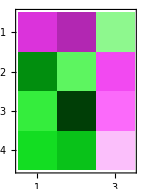

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

### Решение (встроенное)

#### Решение (встроенное)

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[1],x2[1],x3[1]}==Rest@First[data["X"]]},{x1[t],x2[t],x3[t]},{t,1,20}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

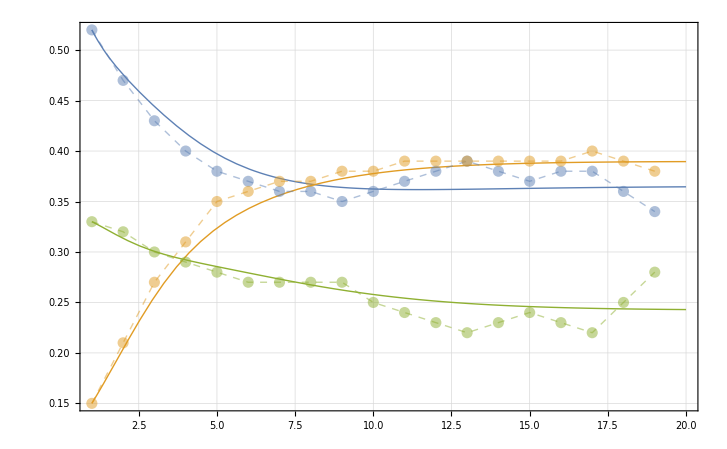

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,1,20},PlotRange->{{1,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]],
ListPlot[Transpose[dataRaw["X"]],Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]
```

### Решение (в точках)

#### Решение (в точках)

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)x_i^(k)
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)x_i^(k)
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)x_i^(k)

{Ln[x_1^(k+1)]-Ln[x_1^(k)]=Δt(b_1+∑_(i=1)^3 A_(i,1)x_i^(k))
Ln[x_2^(k+1)]-Ln[x_2^(k)]=Δt(b_2+∑_(i=1)^3 A_(i,2)x_i^(k))
Ln[x_3^(k+1)]-Ln[x_3^(k)]=Δt(b_3+∑_(i=1)^3 A_(i,3)x_i^(k))

{x_1^(k+1)=Exp[Ln[x_1^(k)]+Δt(b_1+∑_(i=1)^3 A_(i,1)x_i^(k))]
x_2^(k+1)=Exp[Ln[x_2^(k)]+Δt(b_2+∑_(i=1)^3 A_(i,2)x_i^(k))]
x_3^(k+1)=Exp[Ln[x_3^(k)]+Δt(b_3+∑_(i=1)^3 A_(i,3)x_i^(k))], k=0,1,…

```mathematica
ClearAll[solution]
solution[1]=Rest[First[data["X"]]]
solution[k_Integer]:=solution[k]=Exp[Log[solution[k-1]]+1Prepend[solution[k-1],1].A]
```

{0.52,0.15,0.33}

```mathematica
dataRaw["X"]
```

{{0.52,0.15,0.33},{0.47,0.21,0.32},{0.43,0.27,0.3},{0.4,0.31,0.29},{0.38,0.35,0.28},{0.37,0.36,0.27},{0.36,0.37,0.27},{0.36,0.37,0.27},{0.35,0.38,0.27},{0.36,0.38,0.25},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.39,0.39,0.22},{0.38,0.39,0.23},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.38,0.4,0.22},{0.36,0.39,0.25},{0.34,0.38,0.28}}

Воспользуемся тем, что Δt=const

```mathematica
solution/@Range[20]
```

{{0.463087,0.210035,0.315598},{0.436912,0.274124,0.29665},{0.406149,0.316065,0.290502},{0.381632,0.33919,0.286097},{0.368124,0.354944,0.278757},{0.361841,0.366453,0.270605},{0.359479,0.374582,0.263304},{0.359139,0.380125,0.257377},{0.359751,0.383799,0.252825},{0.360715,0.386176,0.249462},{0.361716,0.387677,0.247053},{0.362605,0.388599,0.245374},{0.363329,0.389149,0.244235},{0.363884,0.389463,0.243483},{0.364292,0.389634,0.243},{0.364581,0.389719,0.2427},{0.364778,0.389754,0.242521},{0.364909,0.389764,0.242418},{0.364993,0.38976,0.242364},{0.365045,0.389751,0.242338}}

#### Graph

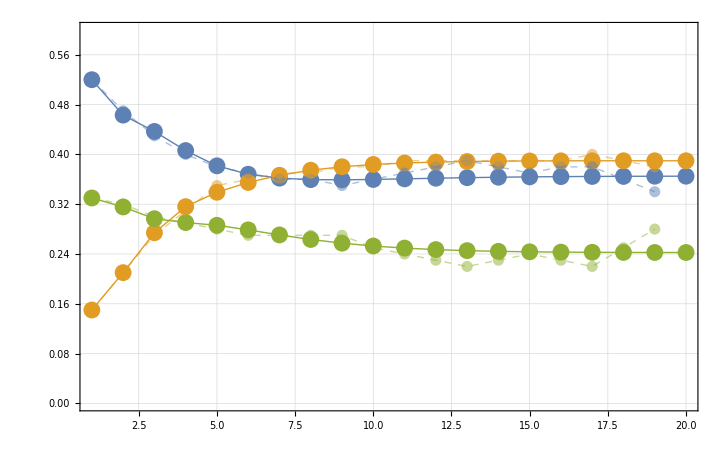

```mathematica
Show[
ListLinePlot[#,PlotRange->{{1,All},{0,0.6}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],Mesh->All],
ListPlot[Transpose[dataRaw["X"]],Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]&[Transpose[solution/@Range[20]]]
```

## Метод Трапеции

## Замена

Применим метод Трапеции

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2, k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,(x_1^(k+1)+x_1^(k))/2,(x_2^(k+1)+x_2^(k))/2,(x_3^(k+1)+x_3^(k))/2]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### data

```mathematica
data=Join[dataRaw,
<|"X"->(Most[#]+Rest[#])/2&[Join[Transpose@{ConstantArray[1,dataRaw["N"]]},dataRaw["X"],2]],
"Δt"->Differences[dataRaw["t"]],
"Y"->Differences[Map[Log,dataRaw["X"],{2}]]/Differences[dataRaw["t"]]
|>]
```

<|names→{Competitor_X,Competitor_Y,Competitor_Z},X→{{1,0.495,0.18,0.325},{1,0.45,0.24,0.31},{1,0.415,0.29,0.295},{1,0.39,0.33,0.285},{1,0.375,0.355,0.275},{1,0.365,0.365,0.27},{1,0.36,0.37,0.27},{1,0.355,0.375,0.27},{1,0.355,0.38,0.26},{1,0.365,0.385,0.245},{1,0.375,0.39,0.235},{1,0.385,0.39,0.225},{1,0.385,0.39,0.225},{1,0.375,0.39,0.235},{1,0.375,0.39,0.235},{1,0.38,0.395,0.225},{1,0.37,0.395,0.235},{1,0.35,0.385,0.265}},t→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},N→19,Δt→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},Y→{{-0.101096,0.336472,-0.0307717},{-0.0889475,0.251314,-0.0645385},{-0.0723207,0.13815,-0.0339016},{-0.0512933,0.121361,-0.0350913},{-0.0266682,0.0281709,-0.0363676},{-0.027399,0.027399,0.},{0.,0.,0.},{-0.0281709,0.0266682,0.},{0.0281709,0.,-0.076961},{0.027399,0.0259755,-0.040822},{0.0266682,0.,-0.0425596},{0.0259755,0.,-0.0444518},{-0.0259755,0.,0.0444518},{-0.0266682,0.,0.0425596},{0.0266682,0.,-0.0425596},{0.,0.0253178,-0.0444518},{-0.0540672,-0.0253178,0.127833},{-0.0571584,-0.0259755,0.113329}}|>

## Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112)

## Principle Components Regression (PCR)

### PCR

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0175685 | 0.0384216 | -0.0067888
-0.00675379 | 0.0147703 | -0.0026098
-0.00624275 | 0.0136527 | -0.00241232
-0.00457193 | 0.00999866 | -0.00176668) | 0.875093
(-0.0235336 | 0.0570527 | -0.0101565
-0.202875 | 0.627325 | -0.113334
0.335508 | -1.05375 | 0.19053
-0.158577 | 0.49101 | -0.0887135) | 0.495541
(-0.043259 | 0.0329178 | -0.00116727
-0.00251503 | 0.872474 | -0.204642
0.345052 | -1.04208 | 0.186181
-0.391788 | 0.205668 | 0.0175649) | 0.493183
(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112) | 0.482945

## Partial least squares regression (PLSR)

### PLSR

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0177483 | 0.0389572 | -0.00688537
-0.00785743 | 0.0172469 | -0.00304825
-0.00450466 | 0.00988766 | -0.00174756
-0.00539977 | 0.0118524 | -0.00209482) | 0.871913
(-0.0231347 | 0.0558238 | -0.00993528
-0.206597 | 0.639566 | -0.11558
0.335064 | -1.05341 | 0.190524
-0.154005 | 0.477183 | -0.0862386) | 0.495493
(-0.0333438 | 0.044238 | -0.005453
-0.0112494 | 0.861255 | -0.201346
0.335028 | -1.05345 | 0.19054
-0.403299 | 0.194273 | 0.023213) | 0.493145
(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112) | 0.482945

## Решение

### A

(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112)

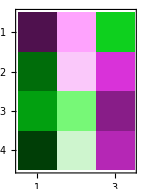

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

### Решение (встроенное)

#### Решение (встроенное)

{(ⅆ X_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[1],x2[1],x3[1]}==First[dataRaw["X"]]},{x1[t],x2[t],x3[t]},{t,1,20}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

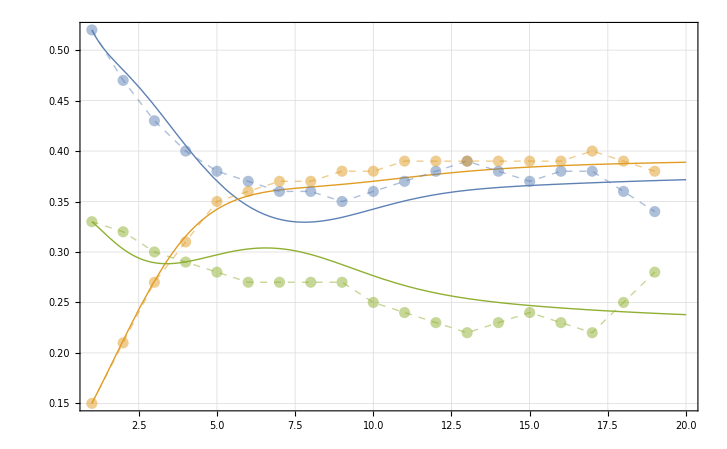

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,1,20},PlotRange->{{1,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]],
ListPlot[Transpose[dataRaw["X"]],Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]
```

### Решение (в точках) (нужно доделать)

#### Решение (в точках)

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2

{Ln[x_1^(k+1)]-Ln[x_1^(k)]=Δt(b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2)
Ln[x_2^(k+1)]-Ln[x_2^(k)]=Δt(b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2)
Ln[x_3^(k+1)]-Ln[x_3^(k)]=Δt(b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2)

{2Ln[x_1^(k+1)]-Δt∑_(i=1)^3 A_(i,1)x_i^(k+1)=2Ln[x_1^(k)]+Δt(2 b_1+∑_(i=1)^3 A_(i,1)x_i^(k))
2Ln[x_2^(k+1)]-Δt∑_(i=1)^3 A_(i,2)x_i^(k+1)=2Ln[x_2^(k)]+Δt(2 b_2+∑_(i=1)^3 A_(i,2)x_i^(k))
2Ln[x_3^(k+1)]-Δt∑_(i=1)^3 A_(i,3)x_i^(k+1)=2Ln[x_3^(k)]+Δt(2 b_3+∑_(i=1)^3 A_(i,3)x_i^(k))

```mathematica
ClearAll[solution]
solution[1]=First[dataRaw["X"]]
solution[k_Integer]:=solution[k]=Exp[Log[solution[k-1]]+1Prepend[solution[k-1],1].A]
```

{0.52,0.15,0.33}

Воспользуемся тем, что Δt=const

```mathematica
solution/@Range[20]
```

{{0.52,0.15,0.33},{0.46248,0.223497,0.305277},{0.442024,0.293195,0.280909},{0.390925,0.344839,0.288096},{0.339418,0.366596,0.309953},{0.305299,0.367527,0.32853},{0.291231,0.361587,0.332358},{0.297364,0.356997,0.317562},{0.322901,0.35749,0.288729},{0.358341,0.364162,0.25882},{0.381358,0.375039,0.241351},{0.381068,0.384734,0.238415},{0.371674,0.389,0.241589},{0.365817,0.389049,0.243707},{0.365714,0.388047,0.242843},{0.368771,0.38776,0.240228},{0.371875,0.388373,0.237636},{0.373538,0.389339,0.235937},{0.374003,0.390142,0.235021},{0.374104,0.390627,0.234427}}

#### Graph

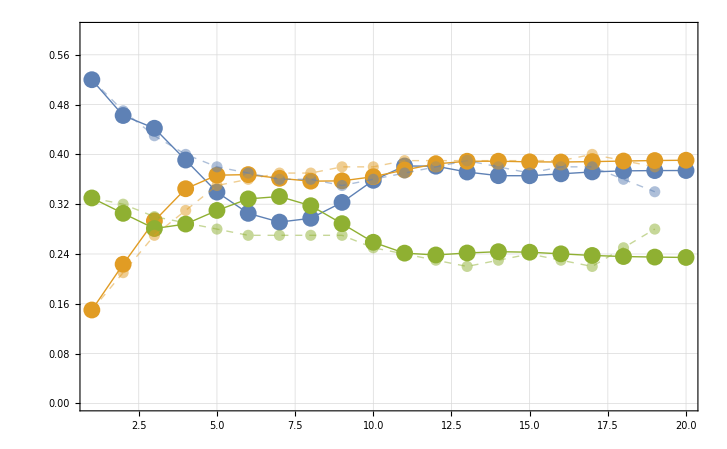

```mathematica
Show[
ListLinePlot[#,PlotRange->{{1,All},{0,0.6}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],Mesh->All],
ListPlot[Transpose[dataRaw["X"]],Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]&[Transpose[solution/@Range[20]]]
```

# Доп

### Задача условной минимизации

Задача условной минимизации появляется тогда, когда известны некоторые ограничения на вектор A